```mathematica
?Reals
```

```mathematica
?Integers
```

```mathematica
?Complexes
```

```mathematica
(**)
```

```mathematica
(*1+1==2*)
```

```mathematica
(*a = 1;
b = 2;*)
```

```mathematica
(*a=== b*)
```

```mathematica
polynomial = (x +1)(x - 1)(x - 2)(x - 3)(x - 4)(x - 4);
```

```mathematica
polynomial==0
```

(-4+x)^2 (-3+x) (-2+x) (-1+x) (1+x)==0

```mathematica
Solve[polynomial==0 , x ]
```

{{x→-1},{x→1},{x→2},{x→3},{x→4},{x→4}}

```mathematica
solution = NSolve[polynomial==0&&x<10&&x>-10 , x]
```

{{x→-1.},{x→1.},{x→2.},{x→3.},{x→4.},{x→4.}}

```mathematica
ReplaceAll[1 + 2 + z , z->1]
```

4

```mathematica
1 + 2 + z/.z->1
```

4

```mathematica
m +2 +z /.{z->1 , m->123}
```

126

```mathematica
solution[[1]]
```

{x→-1.}

```mathematica
x/.solution[[1]]
```

-1.

```mathematica
solution
```

{{x→-1.},{x→1.},{x→2.},{x→3.},{x→4.},{x→4.}}

```mathematica
x/.solution
```

{-1.,1.,2.,3.,4.,4.}

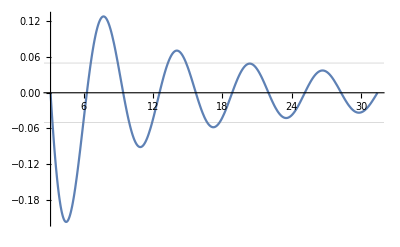

```mathematica
Plot[Sin[x]/x , {x , π , 10π} , GridLines->{None , {-0.05 , 0.05}}]
```

```mathematica
m = {{1 , 2 , 3},{4 , 5 , 6},{7 , 8 , 9}};
```

```mathematica
MatrixForm[m]
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
v = {α , β , γ}
```

{α,β,γ}

```mathematica
m.v
```

{α+2 β+3 γ,4 α+5 β+6 γ,7 α+8 β+9 γ}

```mathematica
m.m//MatrixForm
```

(30 | 36 | 42
66 | 81 | 96
102 | 126 | 150)

```mathematica
MatrixPower[m , 10]//FullSimplify
```

{{132476037840,162775103256,193074168672},{300005963406,368621393481,437236823556},{467535888972,574467683706,681399478440}}

```mathematica
Series[Exp[x] , {x , 0 , 10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
MatrixExp[m]//N//MatrixForm
```

(1.11891×10^6 | 1.37482×10^6 | 1.63072×10^6
2.53388×10^6 | 3.11342×10^6 | 3.69295×10^6
3.94886×10^6 | 4.85201×10^6 | 5.75517×10^6)

```mathematica
aaa={{1 , 1} , {1 , 1}};
```

```mathematica
bbb={{1 , -1} , {-1 , 1}};
```

```mathematica
ccc=1/2 aaa + 3/2 bbb;
```

```mathematica
ccc//MatrixForm
```

(2 | -1
-1 | 2)

```mathematica
Solve[α aaa + β bbb == ccc , {α , β}]
```

{{α→1/2,β→3/2}}

```mathematica
Exp[ⅈ ϕ]//ComplexExpand
```

Cos[ϕ]+ⅈ Sin[ϕ]

```mathematica
f[n_Integer][x_]:=n +x;
```

```mathematica
f[1.23][123]
```

f[1.23][123]

```mathematica
f[1][0]
```

1

```mathematica
Nest[f[1] , 0 , 10]
```

10

```mathematica
(*Jednostkę urojoną wprowadzamy ESC + ii + ESC*)
```

```mathematica
Abs[ⅈ]
```

1

```mathematica
Abs[α + β ⅈ]//ComplexExpand
```

√(α^2+β^2)

```mathematica
α + β ⅈ//Re//ComplexExpand
```

α

```mathematica
α + β ⅈ//Im//ComplexExpand
```

β

```mathematica
I I
```

-1